### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np =5;
d = 1;
lm = 1;
lp[k_]:=((k+1)^-(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
```

-1<k&&Im[k]==0

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

### Normalization and 2RDO Spin sectors

```mathematica
(*the exponential contribution to the particle reduced density operator is determined analytically for the N-particle case as a polynomical (polyefunana with coefficient cp) and also written explicitly for the N=3 case in the efun function*)
```

```mathematica
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
polyefunana[a_,b_,Np_,x1_, x1p_, x2_, x2p_]:= (-a(x1^2+x2^2+x1p^2+x2p^2))+(b((x1+x2)^2+(x1p+x2p)^2))+(cp[a,b,Np]*(x1+x1p+x2+x2p)^2);
```

```mathematica
polyefunana[a,b,4,x1,x1p,x2,x2p]
```

(b^2 (x1+x1p+x2+x2p)^2)/(a-2 b)-a (x1^2+x1p^2+x2^2+x2p^2)+b ((x1+x2)^2+(x1p+x2p)^2)

```mathematica
efun[a_,b_, x1_, x1p_, x2_, x2p_]:=Exp[-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2)-4 a b (x1^2+x1p^2+x1 x2+x2^2+x1p x2p+x2p^2))];
```

```mathematica
(*rho2.. are the polynomial contributions to the 2particle reduced density operators in the various spin sectors. u <-> Up, d <-> Down. If only two spins are specified,e.g. uu then this is a diagonal entry,if 4 spins are specified this is an off-diagonal entry where the two first spins correspond to the ket and the two second spins to the bra, i.e. rho2uddu = ket(ud)*bra(du) *)
```

```mathematica
rho2dd[a_,b_]:=(2 √2 a^3 (a-3 b)^(3/2) (x1-x2) (x1p-x2p) (a+4 a^2 x3^2-4 a b x3 (x1+x1p+x2+x2p+4 x3)+b (-1+b (x1+x1p+x2+x2p+4 x3)^2)))/(3 (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))
rho2uu[a_,b_]:=1/(5 (a-3 b)^4 π)a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b))(x1-x2) (x1p-x2p) (108 b^4+16 a^6 x1 x1p x2 x2p+36 a b^3 (-5+2 b (2 x1^2+2 x1p^2+2 x2^2+7 x2 x2p+2 x2p^2+7 x1p (x2+x2p)+7 x1 (x1p+x2+x2p)))-4 a^5 (-x2 x2p+2 b x1p^2 x2 x2p+x1p (x2+x2p) (-1+2 b x2 x2p)+2 b x1^2 (x2 x2p+x1p (x2+x2p))+x1 (2 b x1p^2 (x2+x2p)+(x2+x2p) (-1+2 b x2 x2p)+x1p (-1+2 b (x2^2+28 x2 x2p+x2p^2))))+a^2 b^2 (111-12 b (13 x1^2+13 x1p^2+13 x2^2+53 x2 x2p+13 x2p^2+53 x1p (x2+x2p)+53 x1 (x1p+x2+x2p))+b^2 (7 x1^4+7 x1p^4+64 x1p^3 (x2+x2p)+64 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (7 x2^2+50 x2 x2p+7 x2p^2)+6 x1p^2 (19 x2^2+80 x2 x2p+19 x2p^2)+32 x1p (2 x2^3+15 x2^2 x2p+15 x2 x2p^2+2 x2p^3)+6 x1^2 (19 x1p^2+19 x2^2+80 x2 x2p+19 x2p^2+80 x1p (x2+x2p))+8 x1 (8 x1p^3+8 x2^3+60 x2^2 x2p+60 x2 x2p^2+8 x2p^3+60 x1p^2 (x2+x2p)+15 x1p (4 x2^2+23 x2 x2p+4 x2p^2))))+a^4 (3-2 b (3 x1^2+3 x1p^2+3 x2^2+28 x2 x2p+3 x2p^2+28 x1p (x2+x2p)+28 x1 (x1p+x2+x2p))+4 b^2 (x1p^3 (x2+x2p)+x2 x2p (x2+x2p)^2+x1^3 (x1p+x2+x2p)+x1p^2 (2 x2^2+23 x2 x2p+2 x2p^2)+x1p (x2^3+23 x2^2 x2p+23 x2 x2p^2+x2p^3)+x1^2 (2 x1p^2+2 x2^2+23 x2 x2p+2 x2p^2+23 x1p (x2+x2p))+x1 (x1p^3+x2^3+23 x2^2 x2p+23 x2 x2p^2+x2p^3+23 x1p^2 (x2+x2p)+x1p (23 x2^2+300 x2 x2p+23 x2p^2))))-2 a^3 b (15-9 b (3 x1^2+3 x1p^2+3 x2^2+16 x2 x2p+3 x2p^2+16 x1p (x2+x2p)+16 x1 (x1p+x2+x2p))+b^2 (x1^4+x1p^4+16 x1p^3 (x2+x2p)+16 x1^3 (x1p+x2+x2p)+30 x1p^2 (x2^2+6 x2 x2p+x2p^2)+(x2+x2p)^2 (x2^2+14 x2 x2p+x2p^2)+4 x1p (4 x2^3+45 x2^2 x2p+45 x2 x2p^2+4 x2p^3)+30 x1^2 (x1p^2+x2^2+6 x2 x2p+x2p^2+6 x1p (x2+x2p))+4 x1 (4 x1p^3+4 x2^3+45 x2^2 x2p+45 x2 x2p^2+4 x2p^3+45 x1p^2 (x2+x2p)+x1p (45 x2^2+366 x2 x2p+45 x2p^2)))))
rho2du[a_,b_] := 1/(20 (a-3 b)^6 π)√((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b))(1296 b^6+64 a^9 x1^2 x1p^2 x2 x2p-162 a b^5 (19+b (5 x1^2-38 x1 x1p+5 x1p^2-17 x2^2-94 x2 x2p-17 x2p^2-36 x1 (x2+x2p)-36 x1p (x2+x2p)))-16 a^8 (x1p^2 x2 x2p+2 b x1^3 x1p (2 x2 x2p+x1p (x2+x2p))+2 x1 x1p x2 x2p (-1+2 b x1p (x1p+x2+x2p))+x1^2 (x2 x2p+2 b x1p^3 (x2+x2p)+4 b x1p x2 x2p (x2+x2p)+x1p^2 (-1+2 b (x2^2+42 x2 x2p+x2p^2))))-18 a^2 b^4 (-159-6 b (35 x1^2-80 x1 x1p+35 x1p^2-65 x1 (x2+x2p)-65 x1p (x2+x2p)-2 (17 x2^2+121 x2 x2p+17 x2p^2))+4 b^2 (13 x1^4+13 x1p^4+105 x1p^3 (x2+x2p)+3 (x2+x2p)^2 (x2^2+5 x2 x2p+x2p^2)+3 x1p^2 (40 x2^2+173 x2 x2p+40 x2p^2)+x1p (31 x2^3+165 x2^2 x2p+165 x2 x2p^2+31 x2p^3)+x1^3 (43 x1p+105 (x2+x2p))+3 x1^2 (-16 x1p^2+40 x2^2+173 x2 x2p+40 x2p^2+117 x1p (x2+x2p))+x1 (43 x1p^3+31 x2^3+165 x2^2 x2p+165 x2 x2p^2+31 x2p^3+351 x1p^2 (x2+x2p)+3 x1p (59 x2^2+124 x2 x2p+59 x2p^2))))+4 a^7 (3 x2 x2p+4 b^2 x1p^4 x2 x2p+2 b x1p^3 (x2+x2p) (1+4 b x2 x2p)+4 b^2 x1^4 (x1p^2+x2 x2p+2 x1p (x2+x2p))+x1p^2 (-1+4 b^2 x2 x2p (x2+x2p)^2+2 b (x2^2+40 x2 x2p+x2p^2))+2 b x1^3 (4 b x1p^3+76 b x1p^2 (x2+x2p)+(x2+x2p) (1+4 b x2 x2p)+2 x1p (-1+b (4 x2^2+74 x2 x2p+4 x2p^2)))+2 x1 x1p (1+b (-2 x1p^2+x1p (x2+x2p)-2 (x2^2+34 x2 x2p+x2p^2))+4 b^2 (x1p^3 (x2+x2p)+2 x2 x2p (x2+x2p)^2+x1p^2 (2 x2^2+37 x2 x2p+2 x2p^2)+x1p (x2^3+38 x2^2 x2p+38 x2 x2p^2+x2p^3)))+x1^2 (-1+2 b (-38 x1p^2+x2^2+40 x2 x2p+x2p^2+x1p (x2+x2p))+4 b^2 (x1p^4+38 x1p^3 (x2+x2p)+x2 x2p (x2+x2p)^2+x1p^2 (39 x2^2+748 x2 x2p+39 x2p^2)+2 x1p (x2^3+38 x2^2 x2p+38 x2 x2p^2+x2p^3))))+a^3 b^3 (-1371+b^3 (7 x1^2+50 x1 x1p+7 x1p^2+8 x1 (x2+x2p)+8 x1p (x2+x2p)+(x2+x2p)^2)^2 (x1^2+x1p^2+7 x2^2+50 x2 x2p+7 x2p^2+8 x1p (x2+x2p)+2 x1 (x1p+4 (x2+x2p)))-9 b (463 x1^2+463 x1p^2-227 x2^2-2146 x2 x2p-227 x2p^2-376 x1p (x2+x2p)-94 x1 (7 x1p+4 (x2+x2p)))+3 b^2 (263 x1^4+263 x1p^4+2992 x1p^3 (x2+x2p)+(x2+x2p)^2 (43 x2^2+302 x2 x2p+43 x2p^2)+54 x1p^2 (61 x2^2+342 x2 x2p+61 x2p^2)+16 x1p (38 x2^3+249 x2^2 x2p+249 x2 x2p^2+38 x2p^3)+4 x1^3 (47 x1p+748 (x2+x2p))+6 x1^2 (-961 x1p^2+1568 x1p (x2+x2p)+9 (61 x2^2+342 x2 x2p+61 x2p^2))+4 x1 (47 x1p^3+2352 x1p^2 (x2+x2p)+27 x1p (33 x2^2+38 x2 x2p+33 x2p^2)+4 (38 x2^3+249 x2^2 x2p+249 x2 x2p^2+38 x2p^3))))-a^6 (-3+6 b (-12 x1^2-12 x1p^2+x2^2+38 x2 x2p+x2p^2+x1p (x2+x2p)+x1 (20 x1p+x2+x2p))-24 b^2 (x1^3 (9 x1p-6 (x2+x2p))+2 x1^2 (49 x1p^2-5 x1p (x2+x2p)-3 (x2^2+19 x2 x2p+x2p^2))-2 x1p (3 x1p^2 (x2+x2p)+x2 x2p (x2+x2p)+3 x1p (x2^2+19 x2 x2p+x2p^2))+x1 (9 x1p^3-10 x1p^2 (x2+x2p)-2 x2 x2p (x2+x2p)+x1p (7 x2^2+150 x2 x2p+7 x2p^2)))+8 b^3 (x1^5 (2 x1p+x2+x2p)+x1^4 (32 x1p^2+3 x2^2+32 x2 x2p+3 x2p^2+61 x1p (x2+x2p))+x1p (x1p+x2+x2p)^2 (x1p^2 (x2+x2p)+2 x2 x2p (x2+x2p)+x1p (x2^2+28 x2 x2p+x2p^2))+x1^3 (60 x1p^3+586 x1p^2 (x2+x2p)+8 x1p (15 x2^2+139 x2 x2p+15 x2p^2)+3 (x2^3+21 x2^2 x2p+21 x2 x2p^2+x2p^3))+x1^2 (32 x1p^4+586 x1p^3 (x2+x2p)+(x2+x2p)^2 (x2^2+32 x2 x2p+x2p^2)+x1p^2 (618 x2^2+7248 x2 x2p+618 x2p^2)+x1p (65 x2^3+1173 x2^2 x2p+1173 x2 x2p^2+65 x2p^3))+x1 (2 x1p^5+61 x1p^4 (x2+x2p)+2 x2 x2p (x2+x2p)^3+4 x1p (x2+x2p)^2 (x2^2+29 x2 x2p+x2p^2)+8 x1p^3 (15 x2^2+139 x2 x2p+15 x2p^2)+x1p^2 (65 x2^3+1173 x2^2 x2p+1173 x2 x2p^2+65 x2p^3))))-a^4 b^2 (-363+6 b (-345 x1^2+438 x1 x1p-345 x1p^2+139 x1 (x2+x2p)+139 x1p (x2+x2p)+4 (25 x2^2+326 x2 x2p+25 x2p^2))+b^2 (219 x1^4+219 x1p^4+4348 x1p^3 (x2+x2p)+(x2+x2p)^2 (19 x2^2+254 x2 x2p+19 x2p^2)+6 x1p^2 (767 x2^2+5962 x2 x2p+767 x2p^2)+12 x1p (41 x2^3+375 x2^2 x2p+375 x2 x2p^2+41 x2p^3)+x1^3 (-1716 x1p+4348 (x2+x2p))-6 x1^2 (3165 x1p^2-767 x2^2-5962 x2 x2p-767 x2p^2-2030 x1p (x2+x2p))-12 x1 (143 x1p^3-41 x2^3-375 x2^2 x2p-375 x2 x2p^2-41 x2p^3-1015 x1p^2 (x2+x2p)+x1p (-191 x2^2+950 x2 x2p-191 x2p^2)))+2 b^3 (14 x1^6+x1^5 (324 x1p+191 (x2+x2p))+x1^4 (2034 x1p^2+517 x2^2+2126 x2 x2p+517 x2p^2+3643 x1p (x2+x2p))+(x1p+x2+x2p)^2 (14 x1p^4+163 x1p^3 (x2+x2p)+(x2+x2p)^2 (x2^2+14 x2 x2p+x2p^2)+3 x1p^2 (59 x2^2+482 x2 x2p+59 x2p^2)+x1p (29 x2^3+327 x2^2 x2p+327 x2 x2p^2+29 x2p^3))+2 x1^3 (1724 x1p^3+9091 x1p^2 (x2+x2p)+2 x1p (1741 x2^2+8246 x2 x2p+1741 x2p^2)+3 (91 x2^3+677 x2^2 x2p+677 x2 x2p^2+91 x2p^3))+2 x1^2 (1017 x1p^4+9091 x1p^3 (x2+x2p)+2 (x2+x2p)^2 (59 x2^2+514 x2 x2p+59 x2p^2)+3 x1p^2 (3373 x2^2+20510 x2 x2p+3373 x2p^2)+21 x1p (103 x2^3+873 x2^2 x2p+873 x2 x2p^2+103 x2p^3))+x1 (324 x1p^5+3643 x1p^4 (x2+x2p)+(x2+x2p)^3 (31 x2^2+326 x2 x2p+31 x2p^2)+8 x1p (x2+x2p)^2 (89 x2^2+790 x2 x2p+89 x2p^2)+4 x1p^3 (1741 x2^2+8246 x2 x2p+1741 x2p^2)+42 x1p^2 (103 x2^3+873 x2^2 x2p+873 x2 x2p^2+103 x2p^3))))+a^5 b (-51+3 b (-179 x1^2+250 x1 x1p-179 x1p^2+31 x2^2+606 x2 x2p+31 x2p^2+36 x1 (x2+x2p)+36 x1p (x2+x2p))+4 b^2 (5 x1^4+5 x1p^4+273 x1p^3 (x2+x2p)+6 x2 x2p (x2+x2p)^2+3 x1p^2 (93 x2^2+1076 x2 x2p+93 x2p^2)+x1p (11 x2^3+189 x2^2 x2p+189 x2 x2p^2+11 x2p^3)+x1^3 (-256 x1p+273 (x2+x2p))+3 x1^2 (-774 x1p^2+93 x2^2+1076 x2 x2p+93 x2p^2+209 x1p (x2+x2p))+x1 (-256 x1p^3+11 x2^3+189 x2^2 x2p+189 x2 x2p^2+11 x2p^3+627 x1p^2 (x2+x2p)-6 x1p (13 x2^2+456 x2 x2p+13 x2p^2)))+4 b^3 (x1^6+4 x1^5 (11 x1p+6 (x2+x2p))+x1^4 (383 x1p^2+68 x2^2+389 x2 x2p+68 x2p^2+704 x1p (x2+x2p))+2 x1^3 (340 x1p^3+35 x2^3+377 x2^2 x2p+377 x2 x2p^2+35 x2p^3+2292 x1p^2 (x2+x2p)+22 x1p (31 x2^2+193 x2 x2p+31 x2p^2))+(x1p+x2+x2p)^2 (x1p^4+22 x1p^3 (x2+x2p)+x2 x2p (x2+x2p)^2+23 x1p^2 (x2^2+13 x2 x2p+x2p^2)+2 x1p (x2^3+22 x2^2 x2p+22 x2 x2p^2+x2p^3))+2 x1 (22 x1p^5+352 x1p^4 (x2+x2p)+(x2+x2p)^3 (x2^2+22 x2 x2p+x2p^2)+2 x1p (x2+x2p)^2 (23 x2^2+319 x2 x2p+23 x2p^2)+22 x1p^3 (31 x2^2+193 x2 x2p+31 x2p^2)+x1p^2 (397 x2^3+4599 x2^2 x2p+4599 x2 x2p^2+397 x2p^3))+x1^2 (383 x1p^4+4584 x1p^3 (x2+x2p)+3 (x2+x2p)^2 (9 x2^2+128 x2 x2p+9 x2p^2)+6 x1p^2 (828 x2^2+6733 x2 x2p+828 x2p^2)+x1p (794 x2^3+9198 x2^2 x2p+9198 x2 x2p^2+794 x2p^3)))))
rho2ud[a_,b_]:=1/(20 (a-3 b)^6 π)√((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b))(1296 b^6+64 a^9 x1 x1p x2^2 x2p^2+162 a b^5 (-19+b (17 x1^2+94 x1 x1p+17 x1p^2-5 x2^2+38 x2 x2p-5 x2p^2+36 x1 (x2+x2p)+36 x1p (x2+x2p)))-16 a^8 (2 b x1^2 x2 x2p (x2 x2p+2 x1p (x2+x2p))+x2^2 x2p^2 (-1+2 b x1p (x1p+x2+x2p))+x1 (4 b x1p^2 x2 x2p (x2+x2p)+2 b x2^2 x2p^2 (x2+x2p)+x1p (x2^2-2 x2 x2p+4 b x2^3 x2p+x2p^2+84 b x2^2 x2p^2+4 b x2 x2p^3)))-18 a^2 b^4 (-159+6 b (34 x1^2+242 x1 x1p+34 x1p^2+65 x1 (x2+x2p)+65 x1p (x2+x2p)-5 (7 x2^2-16 x2 x2p+7 x2p^2))+4 b^2 (3 x1^4+3 x1p^4+13 x2^4+43 x2^3 x2p-48 x2^2 x2p^2+43 x2 x2p^3+13 x2p^4+31 x1p^3 (x2+x2p)+3 x1p^2 (40 x2^2+59 x2 x2p+40 x2p^2)+3 x1p (35 x2^3+117 x2^2 x2p+117 x2 x2p^2+35 x2p^3)+x1^3 (21 x1p+31 (x2+x2p))+3 x1^2 (12 x1p^2+40 x2^2+59 x2 x2p+40 x2p^2+55 x1p (x2+x2p))+3 x1 (7 x1p^3+35 x2^3+117 x2^2 x2p+117 x2 x2p^2+35 x2p^3+55 x1p^2 (x2+x2p)+x1p (173 x2^2+124 x2 x2p+173 x2p^2))))+a^3 b^3 (-1371+9 b (227 x1^2+2146 x1 x1p+227 x1p^2-463 x2^2+658 x2 x2p-463 x2p^2+376 x1 (x2+x2p)+376 x1p (x2+x2p))+b^3 (7 x1^2+50 x1 x1p+7 x1p^2+8 x1 (x2+x2p)+8 x1p (x2+x2p)+(x2+x2p)^2) (x1^2+x1p^2+7 x2^2+50 x2 x2p+7 x2p^2+8 x1p (x2+x2p)+2 x1 (x1p+4 (x2+x2p)))^2+3 b^2 (43 x1^4+43 x1p^4+263 x2^4+188 x2^3 x2p-5766 x2^2 x2p^2+188 x2 x2p^3+263 x2p^4+608 x1p^3 (x2+x2p)+54 x1p^2 (61 x2^2+66 x2 x2p+61 x2p^2)+16 x1p (187 x2^3+588 x2^2 x2p+588 x2 x2p^2+187 x2p^3)+4 x1^3 (97 x1p+152 (x2+x2p))+6 x1^2 (115 x1p^2+664 x1p (x2+x2p)+9 (61 x2^2+66 x2 x2p+61 x2p^2))+4 x1 (97 x1p^3+996 x1p^2 (x2+x2p)+513 x1p (9 x2^2+2 x2 x2p+9 x2p^2)+4 (187 x2^3+588 x2^2 x2p+588 x2 x2p^2+187 x2p^3))))+4 a^7 (4 b^2 x2^4 x2p (2 x1p+x2p)+2 b x2^3 (x1p-2 x2p+8 b x1p^2 x2p+76 b x1p x2p^2+4 b x2p^3)+x2p^2 (-1+2 b x1p (x1p+x2p))+2 x2 x2p (1+4 b^2 x1p x2p (x1p+x2p)^2+b (-2 x1p^2+x1p x2p-2 x2p^2))+4 b^2 x1^3 (2 x2 x2p (x2+x2p)+x1p (x2^2+4 x2 x2p+x2p^2))+x2^2 (-1+2 b (x1p^2+x1p x2p-38 x2p^2)+4 b^2 x2p (2 x1p^3+39 x1p^2 x2p+38 x1p x2p^2+x2p^3))+2 b x1^2 (4 b x2^3 (x1p+2 x2p)+x2p^2 (1+4 b x1p (x1p+x2p))+2 x2 x2p (-1+4 b (2 x1p^2+19 x1p x2p+x2p^2))+x2^2 (1+2 b (2 x1p^2+76 x1p x2p+39 x2p^2)))+x1 (4 b^2 x1p^3 (x2^2+4 x2 x2p+x2p^2)+8 b^2 x1p^2 (x2^3+38 x2^2 x2p+38 x2 x2p^2+x2p^3)+2 b (x2+x2p) (4 b x2^3 x2p+x2p^2+4 b x2 x2p^3+x2^2 (1+72 b x2p^2))+x1p (3+8 b (10 x2^2-17 x2 x2p+10 x2p^2)+4 b^2 (x2^4+74 x2^3 x2p+748 x2^2 x2p^2+74 x2 x2p^3+x2p^4))))-a^6 (-3+6 b (x1^2+x1p^2+x1p (x2+x2p)+x1 (38 x1p+x2+x2p)-4 (3 x2^2-5 x2 x2p+3 x2p^2))+24 b^2 (x1p^2 (6 x2^2-7 x2 x2p+6 x2p^2)-x2 x2p (9 x2^2+98 x2 x2p+9 x2p^2)+2 x1p (3 x2^3+5 x2^2 x2p+5 x2 x2p^2+3 x2p^3)+x1^2 (6 x2^2-7 x2 x2p+6 x2p^2+2 x1p (x2+x2p))+2 x1 (3 x2^3+5 x2^2 x2p+5 x2 x2p^2+3 x2p^3+x1p^2 (x2+x2p)+x1p (57 x2^2-75 x2 x2p+57 x2p^2)))+8 b^3 (x1p^4 (x2^2+4 x2 x2p+x2p^2)+2 x2 x2p (x2+x2p)^2 (x2^2+14 x2 x2p+x2p^2)+x1p^3 (3 x2^3+65 x2^2 x2p+65 x2 x2p^2+3 x2p^3)+3 x1p^2 (x2^4+40 x2^3 x2p+206 x2^2 x2p^2+40 x2 x2p^3+x2p^4)+x1p (x2^5+61 x2^4 x2p+586 x2^3 x2p^2+586 x2^2 x2p^3+61 x2 x2p^4+x2p^5)+x1^4 (x2^2+4 x2 x2p+x2p^2+2 x1p (x2+x2p))+x1^3 (3 x2^3+65 x2^2 x2p+65 x2 x2p^2+3 x2p^3+6 x1p^2 (x2+x2p)+2 x1p (17 x2^2+62 x2 x2p+17 x2p^2))+3 x1^2 (x2^4+40 x2^3 x2p+206 x2^2 x2p^2+40 x2 x2p^3+x2p^4+2 x1p^3 (x2+x2p)+x1p^2 (22 x2^2+80 x2 x2p+22 x2p^2)+x1p (21 x2^3+391 x2^2 x2p+391 x2 x2p^2+21 x2p^3))+x1 (x2^5+61 x2^4 x2p+586 x2^3 x2p^2+586 x2^2 x2p^3+61 x2 x2p^4+x2p^5+2 x1p^4 (x2+x2p)+2 x1p^3 (17 x2^2+62 x2 x2p+17 x2p^2)+3 x1p^2 (21 x2^3+391 x2^2 x2p+391 x2 x2p^2+21 x2p^3)+8 x1p (4 x2^4+139 x2^3 x2p+906 x2^2 x2p^2+139 x2 x2p^3+4 x2p^4))))-a^4 b^2 (-363+6 b (100 x1^2+1304 x1 x1p+100 x1p^2-345 x2^2+438 x2 x2p-345 x2p^2+139 x1 (x2+x2p)+139 x1p (x2+x2p))+b^2 (19 x1^4+19 x1p^4+492 x1p^3 (x2+x2p)+6 x1p^2 (767 x2^2+382 x2 x2p+767 x2p^2)+4 x1p (1087 x2^3+3045 x2^2 x2p+3045 x2 x2p^2+1087 x2p^3)+3 (73 x2^4-572 x2^3 x2p-6330 x2^2 x2p^2-572 x2 x2p^3+73 x2p^4)+4 x1^3 (73 x1p+123 (x2+x2p))+6 x1^2 (91 x1p^2+767 x2^2+382 x2 x2p+767 x2p^2+750 x1p (x2+x2p))+4 x1 (73 x1p^3+1087 x2^3+3045 x2^2 x2p+3045 x2 x2p^2+1087 x2p^3+1125 x1p^2 (x2+x2p)+3 x1p (2981 x2^2-950 x2 x2p+2981 x2p^2)))+2 b^3 (x1^6+x1p^6+31 x1p^5 (x2+x2p)+4 x1p^4 (59 x2^2+178 x2 x2p+59 x2p^2)+42 x1p^3 (13 x2^3+103 x2^2 x2p+103 x2 x2p^2+13 x2p^3)+2 (x2+x2p)^2 (7 x2^4+148 x2^3 x2p+714 x2^2 x2p^2+148 x2 x2p^3+7 x2p^4)+x1p^2 (517 x2^4+6964 x2^3 x2p+20238 x2^2 x2p^2+6964 x2 x2p^3+517 x2p^4)+x1p (191 x2^5+3643 x2^4 x2p+18182 x2^3 x2p^2+18182 x2^2 x2p^3+3643 x2 x2p^4+191 x2p^5)+x1^5 (18 x1p+31 (x2+x2p))+x1^4 (63 x1p^2+419 x1p (x2+x2p)+4 (59 x2^2+178 x2 x2p+59 x2p^2))+2 x1^3 (46 x1p^3+551 x1p^2 (x2+x2p)+16 x1p (79 x2^2+242 x2 x2p+79 x2p^2)+21 (13 x2^3+103 x2^2 x2p+103 x2 x2p^2+13 x2p^3))+x1^2 (63 x1p^4+517 x2^4+6964 x2^3 x2p+20238 x2^2 x2p^2+6964 x2 x2p^3+517 x2p^4+1102 x1p^3 (x2+x2p)+24 x1p^2 (191 x2^2+586 x2 x2p+191 x2p^2)+6 x1p (677 x2^3+6111 x2^2 x2p+6111 x2 x2p^2+677 x2p^3))+x1 (18 x1p^5+191 x2^5+3643 x2^4 x2p+18182 x2^3 x2p^2+18182 x2^2 x2p^3+3643 x2 x2p^4+191 x2p^5+419 x1p^4 (x2+x2p)+32 x1p^3 (79 x2^2+242 x2 x2p+79 x2p^2)+6 x1p^2 (677 x2^3+6111 x2^2 x2p+6111 x2 x2p^2+677 x2p^3)+2 x1p (1063 x2^4+16492 x2^3 x2p+61530 x2^2 x2p^2+16492 x2 x2p^3+1063 x2p^4))))+a^5 b (-51+3 b (31 x1^2+606 x1 x1p+31 x1p^2-179 x2^2+250 x2 x2p-179 x2p^2+36 x1 (x2+x2p)+36 x1p (x2+x2p))+4 b^2 (5 x2^4-256 x2^3 x2p-2322 x2^2 x2p^2-256 x2 x2p^3+5 x2p^4+11 x1p^3 (x2+x2p)+3 x1p^2 (93 x2^2-26 x2 x2p+93 x2p^2)+3 x1p (91 x2^3+209 x2^2 x2p+209 x2 x2p^2+91 x2p^3)+x1^3 (6 x1p+11 (x2+x2p))+3 x1^2 (4 x1p^2+93 x2^2-26 x2 x2p+93 x2p^2+63 x1p (x2+x2p))+3 x1 (2 x1p^3+91 x2^3+209 x2^2 x2p+209 x2 x2p^2+91 x2p^3+63 x1p^2 (x2+x2p)+4 x1p (269 x2^2-228 x2 x2p+269 x2p^2)))+4 b^3 (2 x1p^5 (x2+x2p)+x1p^4 (27 x2^2+92 x2 x2p+27 x2p^2)+x1p^3 (70 x2^3+794 x2^2 x2p+794 x2 x2p^2+70 x2p^3)+(x2+x2p)^2 (x2^4+42 x2^3 x2p+298 x2^2 x2p^2+42 x2 x2p^3+x2p^4)+4 x1p^2 (17 x2^4+341 x2^3 x2p+1242 x2^2 x2p^2+341 x2 x2p^3+17 x2p^4)+8 x1p (3 x2^5+88 x2^4 x2p+573 x2^3 x2p^2+573 x2^2 x2p^3+88 x2 x2p^4+3 x2p^5)+x1^5 (x1p+2 (x2+x2p))+x1^4 (4 x1p^2+27 x2^2+92 x2 x2p+27 x2p^2+50 x1p (x2+x2p))+2 x1^3 (3 x1p^3+35 x2^3+397 x2^2 x2p+397 x2 x2p^2+35 x2p^3+70 x1p^2 (x2+x2p)+73 x1p (3 x2^2+10 x2 x2p+3 x2p^2))+2 x1^2 (2 x1p^4+34 x2^4+682 x2^3 x2p+2484 x2^2 x2p^2+682 x2 x2p^3+34 x2p^4+70 x1p^3 (x2+x2p)+3 x1p^2 (137 x2^2+456 x2 x2p+137 x2p^2)+x1p (377 x2^3+4599 x2^2 x2p+4599 x2 x2p^2+377 x2p^3))+x1 (x1p^5+50 x1p^4 (x2+x2p)+146 x1p^3 (3 x2^2+10 x2 x2p+3 x2p^2)+x1p^2 (754 x2^3+9198 x2^2 x2p+9198 x2 x2p^2+754 x2p^3)+x1p (389 x2^4+8492 x2^3 x2p+40398 x2^2 x2p^2+8492 x2 x2p^3+389 x2p^4)+8 (3 x2^5+88 x2^4 x2p+573 x2^3 x2p^2+573 x2^2 x2p^3+88 x2 x2p^4+3 x2p^5)))))
rho2uddu[a_,b_]:=1/(60 (a-3 b)^6 π)√((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b))(-3888 b^6-64 a^9 x1 x1p x2 x2p (x1p x2+2 x1 x2p)-162 a b^5 (-57+b (7 x1^2+29 x1p^2+226 x1p x2+29 x2^2+108 x1p x2p+108 x2 x2p+7 x2p^2+2 x1 (54 x1p+54 x2+85 x2p)))+16 a^8 (4 b x1^3 x2p (x2 x2p+x1p (2 x2+x2p))+2 x1^2 (b x1p^2 (x2^2+6 x2 x2p+2 x2p^2)+x1p (x2+6 b x2^2 x2p+84 b x2 x2p^2+2 b x2p^3)+x2p^2 (-1+2 b x2 (x2+x2p)))+x1p x2 (2 b x1p^2 x2 x2p+2 x2p^2+x1p x2 (-1+2 b x2p (x2+x2p)))+x1 ((x1p^2-6 x1p x2+x2^2) x2p+2 b x1p x2 (x1p^2 (x2+2 x2p)+2 x2p (x2^2+3 x2 x2p+2 x2p^2)+x1p (x2^2+42 x2 x2p+6 x2p^2))))+18 a^2 b^4 (-477-18 b (12 x1^2-11 x1p^2-188 x1p x2-11 x2^2-65 x1p x2p-65 x2 x2p+12 x2p^2-x1 (65 x1p+65 x2+134 x2p))+4 b^2 (29 x1^4+19 x1p^4+19 x2^4+167 x2^3 x2p+360 x2^2 x2p^2+241 x2 x2p^3+29 x2p^4+x1^3 (241 x1p+241 x2+107 x2p)+x1p^3 (85 x2+167 x2p)+3 x1^2 (120 x1p^2+405 x1p x2+120 x2^2+289 x1p x2p+289 x2 x2p-20 x2p^2)+3 x1p^2 (8 x2^2+227 x2 x2p+120 x2p^2)+x1p (85 x2^3+681 x2^2 x2p+1215 x2 x2p^2+241 x2p^3)+x1 (167 x1p^3+167 x2^3+873 x2^2 x2p+867 x2 x2p^2+107 x2p^3+x1p^2 (681 x2+873 x2p)+3 x1p (227 x2^2+372 x2 x2p+289 x2p^2))))-4 a^7 (-x2^2+2 b x2^3 x2p-2 x2p^2+6 b x2^2 x2p^2+4 b x2 x2p^3+4 b^2 x1p^4 x2 (x2+2 x2p)+8 b^2 x1^4 (x2p (2 x2+x2p)+x1p (x2+2 x2p))+4 b x1^3 (x1p+x2-2 x2p+9 b x2^2 x2p+76 b x2 x2p^2+4 b x2p^3+b x1p^2 (6 x2+9 x2p)+2 b x1p (3 x2^2+76 x2 x2p+38 x2p^2))+2 b x1p^3 (4 b x2^3+x2p+76 b x2^2 x2p+2 x2 (-1+6 b x2p^2))+x1p^2 (-1+b (-76 x2^2+2 x2 x2p+6 x2p^2)+4 b^2 x2 (x2^3+38 x2^2 x2p+43 x2 x2p^2+6 x2p^3))+2 x1p (4 b^2 x2^4 x2p+2 b x2p^3+2 b x2^3 (-1+6 b x2p^2)+b x2^2 x2p (1+12 b x2p^2)+x2 (4+78 b x2p^2+4 b^2 x2p^4))+2 x1^2 (-1+b (3 x1p^2+3 x2^2+2 x2 x2p-76 x2p^2+2 x1p (39 x2+x2p))+2 b^2 (6 x1p^3 (x2+x2p)+x1p^2 (43 x2^2+228 x2 x2p+80 x2p^2)+2 x2p (3 x2^3+40 x2^2 x2p+38 x2 x2p^2+x2p^3)+2 x1p (3 x2^3+114 x2^2 x2p+752 x2 x2p^2+38 x2p^3)))+x1 (7 x2p+2 b (x1p^3+x2^3+36 x2^2 x2p+2 x2 x2p^2-4 x2p^3+x1p^2 (x2+36 x2p)+x1p (x2^2-204 x2 x2p+2 x2p^2))+4 b^2 (x1p^4 (2 x2+x2p)+x2 x2p (x2+x2p)^2 (x2+4 x2p)+x1p^3 (38 x2^2+82 x2 x2p+6 x2p^2)+x1p^2 (38 x2^3+764 x2^2 x2p+228 x2 x2p^2+9 x2p^3)+2 x1p (x2^4+41 x2^3 x2p+114 x2^2 x2p^2+76 x2 x2p^3+2 x2p^4))))+a^6 (-9-6 b (23 x1^2+10 x1p^2+10 x2^2-3 x2 x2p+23 x2p^2-3 x1p (32 x2+x2p)-3 x1 (x1p+x2+26 x2p))+24 b^2 (6 x1^3 (2 x1p+2 x2-3 x2p)+x1p^3 (-9 x2+6 x2p)+x1^2 (18 x1p^2+221 x1p x2+18 x2^2+22 x1p x2p+22 x2 x2p-196 x2p^2)+6 x2 x2p (x2^2+3 x2 x2p+2 x2p^2)+x1p^2 (-98 x2^2+14 x2 x2p+18 x2p^2)+x1p (-9 x2^3+14 x2^2 x2p+221 x2 x2p^2+12 x2p^3)+2 x1 (3 x1p^3+3 x2^3+50 x2^2 x2p+11 x2 x2p^2-9 x2p^3+x1p^2 (7 x2+50 x2p)+x1p (7 x2^2-225 x2 x2p+11 x2p^2)))+8 b^3 (x1p^5 (2 x2+x2p)+x2 x2p (x2+x2p)^3 (x2+2 x2p)+2 x1^5 (x1p+x2+2 x2p)+x1p^4 (32 x2^2+65 x2 x2p+5 x2p^2)+x1^4 (7 x1p^2+68 x1p x2+7 x2^2+124 x1p x2p+124 x2 x2p+64 x2p^2)+x1p (x2+x2p)^2 (2 x2^3+61 x2^2 x2p+64 x2 x2p^2+2 x2p^3)+x1p^3 (60 x2^3+598 x2^2 x2p+188 x2 x2p^2+9 x2p^3)+x1p^2 (32 x2^4+598 x2^3 x2p+750 x2^2 x2p^2+191 x2 x2p^3+7 x2p^4)+x1^3 (9 x1p^3+9 x2^3+274 x2^2 x2p+1178 x2 x2p^2+120 x2p^3+x1p^2 (191 x2+274 x2p)+x1p (191 x2^2+2348 x2 x2p+1178 x2p^2))+x1^2 (5 x1p^4+5 x2^4+193 x2^3 x2p+1302 x2^2 x2p^2+1178 x2 x2p^3+64 x2p^4+x1p^3 (188 x2+193 x2p)+3 x1p^2 (250 x2^2+1173 x2 x2p+434 x2p^2)+x1p (188 x2^3+3519 x2^2 x2p+14736 x2 x2p^2+1178 x2p^3))+x1 (x1p^5+5 x1p^4 (13 x2+8 x2p)+x1p^3 (598 x2^2+1360 x2 x2p+193 x2p^2)+(x2+x2p)^2 (x2^3+38 x2^2 x2p+116 x2 x2p^2+4 x2p^3)+x1p^2 (598 x2^3+7728 x2^2 x2p+3519 x2 x2p^2+274 x2p^3)+x1p (65 x2^4+1360 x2^3 x2p+3519 x2^2 x2p^2+2348 x2 x2p^3+124 x2p^4))))-a^5 b (-153+b (-981 x1^2-351 x1p^2+4386 x1p x2-351 x2^2+324 x1p x2p+324 x2 x2p-981 x2p^2+6 x1 (54 x1p+54 x2+553 x2p))+4 b^2 (10 x1^4+5 x1p^4+5 x2^4+x1^3 (557 x1p+557 x2-506 x2p)+295 x2^3 x2p+837 x2^2 x2p^2+557 x2 x2p^3+10 x2p^4+x1p^3 (-244 x2+295 x2p)+3 x1^2 (279 x1p^2+2126 x1p x2+279 x2^2+481 x1p x2p+481 x2 x2p-1544 x2p^2)+x1p^2 (-2298 x2^2+1005 x2 x2p+837 x2p^2)+x1p (-244 x2^3+1005 x2^2 x2p+6378 x2 x2p^2+557 x2p^3)+x1 (295 x1p^3+295 x2^3+3072 x2^2 x2p+1443 x2 x2p^2-506 x2p^3+3 x1p^2 (335 x2+1024 x2p)+3 x1p (335 x2^2-2736 x2 x2p+481 x2p^2)))+4 b^3 (2 x1^6+x1p^6+x1p^5 (46 x2+28 x2p)+x1^5 (50 x1p+50 x2+89 x2p)+x1p^4 (391 x2^2+804 x2 x2p+122 x2p^2)+x1^4 (163 x1p^2+870 x1p x2+163 x2^2+1458 x1p x2p+1458 x2 x2p+770 x2p^2)+(x2+x2p)^3 (x2^3+25 x2^2 x2p+44 x2 x2p^2+2 x2p^3)+2 x1p (x2+x2p)^2 (23 x2^3+356 x2^2 x2p+385 x2 x2p^2+25 x2p^3)+x1p^3 (692 x2^3+4864 x2^2 x2p+2240 x2 x2p^2+210 x2p^3)+x1p^2 (391 x2^4+4864 x2^3 x2p+6612 x2^2 x2p^2+2302 x2 x2p^3+163 x2p^4)+2 x1^3 (105 x1p^3+105 x2^3+1583 x2^2 x2p+4654 x2 x2p^2+683 x2p^3+x1p^2 (1151 x2+1583 x2p)+x1p (1151 x2^2+9222 x2 x2p+4654 x2p^2))+2 x1^2 (61 x1p^4+61 x2^4+1171 x2^3 x2p+5379 x2^2 x2p^2+4654 x2 x2p^3+385 x2p^4+x1p^3 (1120 x2+1171 x2p)+3 x1p^2 (1102 x2^2+4599 x2 x2p+1793 x2p^2)+x1p (1120 x2^3+13797 x2^2 x2p+41766 x2 x2p^2+4654 x2p^3))+x1 (28 x1p^5+x1p^4 (804 x2+573 x2p)+2 x1p^3 (2432 x2^2+5706 x2 x2p+1171 x2p^2)+(x2+x2p)^2 (28 x2^3+517 x2^2 x2p+1280 x2 x2p^2+89 x2p^3)+x1p^2 (4864 x2^3+45870 x2^2 x2p+27594 x2 x2p^2+3166 x2p^3)+6 x1p (134 x2^4+1902 x2^3 x2p+4599 x2^2 x2p^2+3074 x2 x2p^3+243 x2p^4))))-3 a^3 b^3 (-1371-9 b (233 x1^2+3 x1p^2+3 x2^2-376 x2 x2p+233 x2p^2-2 x1p (825 x2+188 x2p)-2 x1 (188 x1p+188 x2+577 x2p))+b^2 (569 x1^4+349 x1p^4+349 x2^4+4208 x2^3 x2p+9882 x2^2 x2p^2+6592 x2 x2p^3+569 x2p^4+x1^3 (6592 x1p+6592 x2+764 x2p)+x1p^3 (964 x2+4208 x2p)+x1p^2 (-4386 x2^2+17376 x2 x2p+9882 x2p^2)+4 x1p (241 x2^3+4344 x2^2 x2p+10125 x2 x2p^2+1648 x2p^3)+6 x1^2 (1647 x1p^2+1647 x2^2+3800 x2 x2p-1807 x2p^2+50 x1p (135 x2+76 x2p))+4 x1 (1052 x1p^3+1052 x2^3+6399 x2^2 x2p+5700 x2 x2p^2+191 x2p^3+x1p^2 (4344 x2+6399 x2p)+6 x1p (724 x2^2+513 x2 x2p+950 x2p^2)))+b^3 (35 x1^6+21 x1p^6+x1p^5 (318 x2+248 x2p)+x1^5 (376 x1p+376 x2+558 x2p)+x1p^4 (1515 x2^2+3160 x2 x2p+889 x2p^2)+x1^4 (1103 x1p^2+3550 x1p x2+1103 x2^2+5144 x1p x2p+5144 x2 x2p+2781 x2p^2)+(x2+x2p)^3 (21 x2^3+185 x2^2 x2p+271 x2 x2p^2+35 x2p^3)+2 x1p (x2+x2p)^2 (159 x2^3+1262 x2^2 x2p+1399 x2 x2p^2+188 x2p^3)+4 x1p^3 (609 x2^3+2924 x2^2 x2p+2041 x2 x2p^2+356 x2p^3)+x1p^2 (1515 x2^4+11696 x2^3 x2p+17574 x2^2 x2p^2+8496 x2 x2p^3+1103 x2p^4)+4 x1^3 (356 x1p^3+356 x2^3+2705 x2^2 x2p+5116 x2 x2p^2+1129 x2p^3+x1p^2 (2124 x2+2705 x2p)+x1p (2124 x2^2+9994 x2 x2p+5116 x2p^2))+x1^2 (889 x1p^4+889 x2^4+8688 x2^3 x2p+25482 x2^2 x2p^2+20464 x2 x2p^3+2781 x2p^4+x1p^3 (8164 x2+8688 x2p)+6 x1p^2 (2929 x2^2+9912 x2 x2p+4247 x2p^2)+4 x1p (2041 x2^3+14868 x2^2 x2p+29013 x2 x2p^2+5116 x2p^3))+2 x1 (124 x1p^5+x1p^4 (1580 x2+1351 x2p)+4 x1p^3 (1462 x2^2+3475 x2 x2p+1086 x2p^2)+(x2+x2p)^2 (124 x2^3+1103 x2^2 x2p+2014 x2 x2p^2+279 x2p^3)+x1p^2 (5848 x2^3+35898 x2^2 x2p+29736 x2 x2p^2+5410 x2p^3)+4 x1p (395 x2^4+3475 x2^3 x2p+7434 x2^2 x2p^2+4997 x2 x2p^3+643 x2p^4))))+a^4 b^2 (-1089-6 b (590 x1^2+145 x1p^2-3046 x1p x2+145 x2^2-417 x1p x2p-417 x2 x2p+590 x2p^2-x1 (417 x1p+417 x2+2180 x2p))+b^2 (457 x1^4+257 x1p^4+257 x2^4+4 x1^3 (2297 x1p+2297 x2-785 x2p)+5332 x2^3 x2p+13806 x2^2 x2p^2+9188 x2 x2p^3+457 x2p^4+x1p^3 (-1132 x2+5332 x2p)+6 x1^2 (2301 x1p^2+12306 x1p x2+2301 x2^2+4810 x1p x2p+4810 x2 x2p-6239 x2p^2)-6 x1p^2 (2983 x2^2-3530 x2 x2p-2301 x2p^2)+x1p (-1132 x2^3+21180 x2^2 x2p+73836 x2 x2p^2+9188 x2p^3)+4 x1 (1333 x1p^3+1333 x2^3+10089 x2^2 x2p+7215 x2 x2p^2-785 x2p^3+3 x1p^2 (1765 x2+3363 x2p)+15 x1p (353 x2^2-570 x2 x2p+481 x2p^2)))+2 b^3 (29 x1^6+16 x1p^6+x1p^5 (360 x2+253 x2p)+x1^5 (413 x1p+413 x2+666 x2p)+x1p^4 (2160 x2^2+4481 x2 x2p+989 x2p^2)+x1^4 (1270 x1p^2+4964 x1p x2+1270 x2^2+7705 x1p x2p+7705 x2 x2p+4131 x2p^2)+(x2+x2p)^3 (16 x2^3+205 x2^2 x2p+326 x2 x2p^2+29 x2p^3)+x1p (x2+x2p)^2 (360 x2^3+3761 x2^2 x2p+4138 x2 x2p^2+413 x2p^3)+2 x1p^3 (1816 x2^3+10193 x2^2 x2p+6010 x2 x2p^2+819 x2p^3)+2 x1p^2 (1080 x2^4+10193 x2^3 x2p+14703 x2^2 x2p^2+6225 x2 x2p^3+635 x2p^4)+2 x1^3 (819 x1p^3+819 x2^3+8228 x2^2 x2p+18733 x2 x2p^2+3494 x2p^3+x1p^2 (6225 x2+8228 x2p)+x1p (6225 x2^2+36856 x2 x2p+18733 x2p^2))+x1^2 (989 x1p^4+989 x2^4+12714 x2^3 x2p+45060 x2^2 x2p^2+37466 x2 x2p^3+4131 x2p^4+2 x1p^3 (6010 x2+6357 x2p)+6 x1p^2 (4901 x2^2+18333 x2 x2p+7510 x2p^2)+2 x1p (6010 x2^3+54999 x2^2 x2p+130092 x2 x2p^2+18733 x2p^3))+x1 (253 x1p^5+x1p^4 (4481 x2+3550 x2p)+2 x1p^3 (10193 x2^2+24236 x2 x2p+6357 x2p^2)+(x2+x2p)^2 (253 x2^3+3044 x2^2 x2p+6373 x2 x2p^2+666 x2p^3)+2 x1p^2 (10193 x2^3+75594 x2^2 x2p+54999 x2 x2p^2+8228 x2p^3)+x1p (4481 x2^4+48472 x2^3 x2p+109998 x2^2 x2p^2+73712 x2 x2p^3+7705 x2p^4)))))
rho2duud[a_,b_]:=1/(60 (a-3 b)^6 π)√((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b))(-3888 b^6-64 a^9 x1 x1p x2 x2p (x1p x2+2 x1 x2p)-162 a b^5 (-57+b (7 x1^2+29 x1p^2+226 x1p x2+29 x2^2+108 x1p x2p+108 x2 x2p+7 x2p^2+2 x1 (54 x1p+54 x2+85 x2p)))+16 a^8 (4 b x1^3 x2p (x2 x2p+x1p (2 x2+x2p))+2 x1^2 (b x1p^2 (x2^2+6 x2 x2p+2 x2p^2)+x1p (x2+6 b x2^2 x2p+84 b x2 x2p^2+2 b x2p^3)+x2p^2 (-1+2 b x2 (x2+x2p)))+x1p x2 (2 b x1p^2 x2 x2p+2 x2p^2+x1p x2 (-1+2 b x2p (x2+x2p)))+x1 ((x1p^2-6 x1p x2+x2^2) x2p+2 b x1p x2 (x1p^2 (x2+2 x2p)+2 x2p (x2^2+3 x2 x2p+2 x2p^2)+x1p (x2^2+42 x2 x2p+6 x2p^2))))+18 a^2 b^4 (-477-18 b (12 x1^2-11 x1p^2-188 x1p x2-11 x2^2-65 x1p x2p-65 x2 x2p+12 x2p^2-x1 (65 x1p+65 x2+134 x2p))+4 b^2 (29 x1^4+19 x1p^4+19 x2^4+167 x2^3 x2p+360 x2^2 x2p^2+241 x2 x2p^3+29 x2p^4+x1^3 (241 x1p+241 x2+107 x2p)+x1p^3 (85 x2+167 x2p)+3 x1^2 (120 x1p^2+405 x1p x2+120 x2^2+289 x1p x2p+289 x2 x2p-20 x2p^2)+3 x1p^2 (8 x2^2+227 x2 x2p+120 x2p^2)+x1p (85 x2^3+681 x2^2 x2p+1215 x2 x2p^2+241 x2p^3)+x1 (167 x1p^3+167 x2^3+873 x2^2 x2p+867 x2 x2p^2+107 x2p^3+x1p^2 (681 x2+873 x2p)+3 x1p (227 x2^2+372 x2 x2p+289 x2p^2))))-4 a^7 (-x2^2+2 b x2^3 x2p-2 x2p^2+6 b x2^2 x2p^2+4 b x2 x2p^3+4 b^2 x1p^4 x2 (x2+2 x2p)+8 b^2 x1^4 (x2p (2 x2+x2p)+x1p (x2+2 x2p))+4 b x1^3 (x1p+x2-2 x2p+9 b x2^2 x2p+76 b x2 x2p^2+4 b x2p^3+b x1p^2 (6 x2+9 x2p)+2 b x1p (3 x2^2+76 x2 x2p+38 x2p^2))+2 b x1p^3 (4 b x2^3+x2p+76 b x2^2 x2p+2 x2 (-1+6 b x2p^2))+x1p^2 (-1+b (-76 x2^2+2 x2 x2p+6 x2p^2)+4 b^2 x2 (x2^3+38 x2^2 x2p+43 x2 x2p^2+6 x2p^3))+2 x1p (4 b^2 x2^4 x2p+2 b x2p^3+2 b x2^3 (-1+6 b x2p^2)+b x2^2 x2p (1+12 b x2p^2)+x2 (4+78 b x2p^2+4 b^2 x2p^4))+2 x1^2 (-1+b (3 x1p^2+3 x2^2+2 x2 x2p-76 x2p^2+2 x1p (39 x2+x2p))+2 b^2 (6 x1p^3 (x2+x2p)+x1p^2 (43 x2^2+228 x2 x2p+80 x2p^2)+2 x2p (3 x2^3+40 x2^2 x2p+38 x2 x2p^2+x2p^3)+2 x1p (3 x2^3+114 x2^2 x2p+752 x2 x2p^2+38 x2p^3)))+x1 (7 x2p+2 b (x1p^3+x2^3+36 x2^2 x2p+2 x2 x2p^2-4 x2p^3+x1p^2 (x2+36 x2p)+x1p (x2^2-204 x2 x2p+2 x2p^2))+4 b^2 (x1p^4 (2 x2+x2p)+x2 x2p (x2+x2p)^2 (x2+4 x2p)+x1p^3 (38 x2^2+82 x2 x2p+6 x2p^2)+x1p^2 (38 x2^3+764 x2^2 x2p+228 x2 x2p^2+9 x2p^3)+2 x1p (x2^4+41 x2^3 x2p+114 x2^2 x2p^2+76 x2 x2p^3+2 x2p^4))))+a^6 (-9-6 b (23 x1^2+10 x1p^2+10 x2^2-3 x2 x2p+23 x2p^2-3 x1p (32 x2+x2p)-3 x1 (x1p+x2+26 x2p))+24 b^2 (6 x1^3 (2 x1p+2 x2-3 x2p)+x1p^3 (-9 x2+6 x2p)+x1^2 (18 x1p^2+221 x1p x2+18 x2^2+22 x1p x2p+22 x2 x2p-196 x2p^2)+6 x2 x2p (x2^2+3 x2 x2p+2 x2p^2)+x1p^2 (-98 x2^2+14 x2 x2p+18 x2p^2)+x1p (-9 x2^3+14 x2^2 x2p+221 x2 x2p^2+12 x2p^3)+2 x1 (3 x1p^3+3 x2^3+50 x2^2 x2p+11 x2 x2p^2-9 x2p^3+x1p^2 (7 x2+50 x2p)+x1p (7 x2^2-225 x2 x2p+11 x2p^2)))+8 b^3 (x1p^5 (2 x2+x2p)+x2 x2p (x2+x2p)^3 (x2+2 x2p)+2 x1^5 (x1p+x2+2 x2p)+x1p^4 (32 x2^2+65 x2 x2p+5 x2p^2)+x1^4 (7 x1p^2+68 x1p x2+7 x2^2+124 x1p x2p+124 x2 x2p+64 x2p^2)+x1p (x2+x2p)^2 (2 x2^3+61 x2^2 x2p+64 x2 x2p^2+2 x2p^3)+x1p^3 (60 x2^3+598 x2^2 x2p+188 x2 x2p^2+9 x2p^3)+x1p^2 (32 x2^4+598 x2^3 x2p+750 x2^2 x2p^2+191 x2 x2p^3+7 x2p^4)+x1^3 (9 x1p^3+9 x2^3+274 x2^2 x2p+1178 x2 x2p^2+120 x2p^3+x1p^2 (191 x2+274 x2p)+x1p (191 x2^2+2348 x2 x2p+1178 x2p^2))+x1^2 (5 x1p^4+5 x2^4+193 x2^3 x2p+1302 x2^2 x2p^2+1178 x2 x2p^3+64 x2p^4+x1p^3 (188 x2+193 x2p)+3 x1p^2 (250 x2^2+1173 x2 x2p+434 x2p^2)+x1p (188 x2^3+3519 x2^2 x2p+14736 x2 x2p^2+1178 x2p^3))+x1 (x1p^5+5 x1p^4 (13 x2+8 x2p)+x1p^3 (598 x2^2+1360 x2 x2p+193 x2p^2)+(x2+x2p)^2 (x2^3+38 x2^2 x2p+116 x2 x2p^2+4 x2p^3)+x1p^2 (598 x2^3+7728 x2^2 x2p+3519 x2 x2p^2+274 x2p^3)+x1p (65 x2^4+1360 x2^3 x2p+3519 x2^2 x2p^2+2348 x2 x2p^3+124 x2p^4))))-a^5 b (-153+b (-981 x1^2-351 x1p^2+4386 x1p x2-351 x2^2+324 x1p x2p+324 x2 x2p-981 x2p^2+6 x1 (54 x1p+54 x2+553 x2p))+4 b^2 (10 x1^4+5 x1p^4+5 x2^4+x1^3 (557 x1p+557 x2-506 x2p)+295 x2^3 x2p+837 x2^2 x2p^2+557 x2 x2p^3+10 x2p^4+x1p^3 (-244 x2+295 x2p)+3 x1^2 (279 x1p^2+2126 x1p x2+279 x2^2+481 x1p x2p+481 x2 x2p-1544 x2p^2)+x1p^2 (-2298 x2^2+1005 x2 x2p+837 x2p^2)+x1p (-244 x2^3+1005 x2^2 x2p+6378 x2 x2p^2+557 x2p^3)+x1 (295 x1p^3+295 x2^3+3072 x2^2 x2p+1443 x2 x2p^2-506 x2p^3+3 x1p^2 (335 x2+1024 x2p)+3 x1p (335 x2^2-2736 x2 x2p+481 x2p^2)))+4 b^3 (2 x1^6+x1p^6+x1p^5 (46 x2+28 x2p)+x1^5 (50 x1p+50 x2+89 x2p)+x1p^4 (391 x2^2+804 x2 x2p+122 x2p^2)+x1^4 (163 x1p^2+870 x1p x2+163 x2^2+1458 x1p x2p+1458 x2 x2p+770 x2p^2)+(x2+x2p)^3 (x2^3+25 x2^2 x2p+44 x2 x2p^2+2 x2p^3)+2 x1p (x2+x2p)^2 (23 x2^3+356 x2^2 x2p+385 x2 x2p^2+25 x2p^3)+x1p^3 (692 x2^3+4864 x2^2 x2p+2240 x2 x2p^2+210 x2p^3)+x1p^2 (391 x2^4+4864 x2^3 x2p+6612 x2^2 x2p^2+2302 x2 x2p^3+163 x2p^4)+2 x1^3 (105 x1p^3+105 x2^3+1583 x2^2 x2p+4654 x2 x2p^2+683 x2p^3+x1p^2 (1151 x2+1583 x2p)+x1p (1151 x2^2+9222 x2 x2p+4654 x2p^2))+2 x1^2 (61 x1p^4+61 x2^4+1171 x2^3 x2p+5379 x2^2 x2p^2+4654 x2 x2p^3+385 x2p^4+x1p^3 (1120 x2+1171 x2p)+3 x1p^2 (1102 x2^2+4599 x2 x2p+1793 x2p^2)+x1p (1120 x2^3+13797 x2^2 x2p+41766 x2 x2p^2+4654 x2p^3))+x1 (28 x1p^5+x1p^4 (804 x2+573 x2p)+2 x1p^3 (2432 x2^2+5706 x2 x2p+1171 x2p^2)+(x2+x2p)^2 (28 x2^3+517 x2^2 x2p+1280 x2 x2p^2+89 x2p^3)+x1p^2 (4864 x2^3+45870 x2^2 x2p+27594 x2 x2p^2+3166 x2p^3)+6 x1p (134 x2^4+1902 x2^3 x2p+4599 x2^2 x2p^2+3074 x2 x2p^3+243 x2p^4))))-3 a^3 b^3 (-1371-9 b (233 x1^2+3 x1p^2+3 x2^2-376 x2 x2p+233 x2p^2-2 x1p (825 x2+188 x2p)-2 x1 (188 x1p+188 x2+577 x2p))+b^2 (569 x1^4+349 x1p^4+349 x2^4+4208 x2^3 x2p+9882 x2^2 x2p^2+6592 x2 x2p^3+569 x2p^4+x1^3 (6592 x1p+6592 x2+764 x2p)+x1p^3 (964 x2+4208 x2p)+x1p^2 (-4386 x2^2+17376 x2 x2p+9882 x2p^2)+4 x1p (241 x2^3+4344 x2^2 x2p+10125 x2 x2p^2+1648 x2p^3)+6 x1^2 (1647 x1p^2+1647 x2^2+3800 x2 x2p-1807 x2p^2+50 x1p (135 x2+76 x2p))+4 x1 (1052 x1p^3+1052 x2^3+6399 x2^2 x2p+5700 x2 x2p^2+191 x2p^3+x1p^2 (4344 x2+6399 x2p)+6 x1p (724 x2^2+513 x2 x2p+950 x2p^2)))+b^3 (35 x1^6+21 x1p^6+x1p^5 (318 x2+248 x2p)+x1^5 (376 x1p+376 x2+558 x2p)+x1p^4 (1515 x2^2+3160 x2 x2p+889 x2p^2)+x1^4 (1103 x1p^2+3550 x1p x2+1103 x2^2+5144 x1p x2p+5144 x2 x2p+2781 x2p^2)+(x2+x2p)^3 (21 x2^3+185 x2^2 x2p+271 x2 x2p^2+35 x2p^3)+2 x1p (x2+x2p)^2 (159 x2^3+1262 x2^2 x2p+1399 x2 x2p^2+188 x2p^3)+4 x1p^3 (609 x2^3+2924 x2^2 x2p+2041 x2 x2p^2+356 x2p^3)+x1p^2 (1515 x2^4+11696 x2^3 x2p+17574 x2^2 x2p^2+8496 x2 x2p^3+1103 x2p^4)+4 x1^3 (356 x1p^3+356 x2^3+2705 x2^2 x2p+5116 x2 x2p^2+1129 x2p^3+x1p^2 (2124 x2+2705 x2p)+x1p (2124 x2^2+9994 x2 x2p+5116 x2p^2))+x1^2 (889 x1p^4+889 x2^4+8688 x2^3 x2p+25482 x2^2 x2p^2+20464 x2 x2p^3+2781 x2p^4+x1p^3 (8164 x2+8688 x2p)+6 x1p^2 (2929 x2^2+9912 x2 x2p+4247 x2p^2)+4 x1p (2041 x2^3+14868 x2^2 x2p+29013 x2 x2p^2+5116 x2p^3))+2 x1 (124 x1p^5+x1p^4 (1580 x2+1351 x2p)+4 x1p^3 (1462 x2^2+3475 x2 x2p+1086 x2p^2)+(x2+x2p)^2 (124 x2^3+1103 x2^2 x2p+2014 x2 x2p^2+279 x2p^3)+x1p^2 (5848 x2^3+35898 x2^2 x2p+29736 x2 x2p^2+5410 x2p^3)+4 x1p (395 x2^4+3475 x2^3 x2p+7434 x2^2 x2p^2+4997 x2 x2p^3+643 x2p^4))))+a^4 b^2 (-1089-6 b (590 x1^2+145 x1p^2-3046 x1p x2+145 x2^2-417 x1p x2p-417 x2 x2p+590 x2p^2-x1 (417 x1p+417 x2+2180 x2p))+b^2 (457 x1^4+257 x1p^4+257 x2^4+4 x1^3 (2297 x1p+2297 x2-785 x2p)+5332 x2^3 x2p+13806 x2^2 x2p^2+9188 x2 x2p^3+457 x2p^4+x1p^3 (-1132 x2+5332 x2p)+6 x1^2 (2301 x1p^2+12306 x1p x2+2301 x2^2+4810 x1p x2p+4810 x2 x2p-6239 x2p^2)-6 x1p^2 (2983 x2^2-3530 x2 x2p-2301 x2p^2)+x1p (-1132 x2^3+21180 x2^2 x2p+73836 x2 x2p^2+9188 x2p^3)+4 x1 (1333 x1p^3+1333 x2^3+10089 x2^2 x2p+7215 x2 x2p^2-785 x2p^3+3 x1p^2 (1765 x2+3363 x2p)+15 x1p (353 x2^2-570 x2 x2p+481 x2p^2)))+2 b^3 (29 x1^6+16 x1p^6+x1p^5 (360 x2+253 x2p)+x1^5 (413 x1p+413 x2+666 x2p)+x1p^4 (2160 x2^2+4481 x2 x2p+989 x2p^2)+x1^4 (1270 x1p^2+4964 x1p x2+1270 x2^2+7705 x1p x2p+7705 x2 x2p+4131 x2p^2)+(x2+x2p)^3 (16 x2^3+205 x2^2 x2p+326 x2 x2p^2+29 x2p^3)+x1p (x2+x2p)^2 (360 x2^3+3761 x2^2 x2p+4138 x2 x2p^2+413 x2p^3)+2 x1p^3 (1816 x2^3+10193 x2^2 x2p+6010 x2 x2p^2+819 x2p^3)+2 x1p^2 (1080 x2^4+10193 x2^3 x2p+14703 x2^2 x2p^2+6225 x2 x2p^3+635 x2p^4)+2 x1^3 (819 x1p^3+819 x2^3+8228 x2^2 x2p+18733 x2 x2p^2+3494 x2p^3+x1p^2 (6225 x2+8228 x2p)+x1p (6225 x2^2+36856 x2 x2p+18733 x2p^2))+x1^2 (989 x1p^4+989 x2^4+12714 x2^3 x2p+45060 x2^2 x2p^2+37466 x2 x2p^3+4131 x2p^4+2 x1p^3 (6010 x2+6357 x2p)+6 x1p^2 (4901 x2^2+18333 x2 x2p+7510 x2p^2)+2 x1p (6010 x2^3+54999 x2^2 x2p+130092 x2 x2p^2+18733 x2p^3))+x1 (253 x1p^5+x1p^4 (4481 x2+3550 x2p)+2 x1p^3 (10193 x2^2+24236 x2 x2p+6357 x2p^2)+(x2+x2p)^2 (253 x2^3+3044 x2^2 x2p+6373 x2 x2p^2+666 x2p^3)+2 x1p^2 (10193 x2^3+75594 x2^2 x2p+54999 x2 x2p^2+8228 x2p^3)+x1p (4481 x2^4+48472 x2^3 x2p+109998 x2^2 x2p^2+73712 x2 x2p^3+7705 x2p^4)))))
rho2ddi[lm_,lp_,Np_]:=rho2dd[A[lp],B[lm,lp, Np]]
rho2udi[lm_,lp_,Np_]:=rho2ud[A[lp],B[lm,lp, Np]]
rho2dui[lm_,lp_,Np_]:=rho2du[A[lp],B[lm,lp, Np]]
rho2uddui[lm_,lp_,Np_]:=rho2uddu[A[lp],B[lm,lp, Np]]
rho2duudi[lm_,lp_,Np_]:=rho2duud[A[lp],B[lm,lp, Np]]
```

```mathematica
(*define 2 particle hf basis*)
(*modes are always defined such that for multi spin basis m1 has spin UP and m2 has spin DOWN, the exponential factor of the Hermite function is included in the exppolyinit variable, here we are only interested in the polynomial contribution of the hf basis*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hfbasisud[m1_, m2_,a_, x1_, x2_]:=1/Sqrt[2](hfcoef[m1,x1,a]*hfcoef[m2,x2, a])
hfbasisdu[m1_, m2_,a_,  x1_, x2_]:=1/Sqrt[2](-hfcoef[m1,x2,a]*hfcoef[m2,x1, a])
hfbasis[m1_, m2_, a_, x1_, x2_]:=1/Sqrt[2]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2, a]}, {hfcoef[m2,x1,a],hfcoef[m2,x2, a]}}]
```

### Determining the coefficients of the Polynomial Contribution to the integral of the 2 - RDO

```mathematica
(*Determine the coefficients of the polynomial 'hfbasis' *rho2.. by the coefficientlist function where q corresponds to the power of the particular variable, i.e. x^q !NOTE! this is not the same as the index Mathematica gives the in the CoefficientList function, *)
```

```mathematica
(*polystart.. denotes the spin component of the polynomial which is comprised of the hermite basis functions and the polynomial contribution of the corresponding spin sector of the 2particle RDO. This is then used in the algorithm in "Running the algorithm" to calculates the integral which is a combination of a polynomial*gaussian exponential*)
```

```mathematica
polystartdd[mode1_, mode2_]:=hfbasis[mode1,mode2, a, x1, x2]*hfbasis[mode1,mode2, a, x1p, x2p]*rho2dd[a,b]
```

```mathematica
(*polystartdd[1,2]*)
```

```mathematica
(*polystartuu[mode1_, mode2_]:=hfbasis[mode1,mode2, a, x1, x2]*hfbasis[mode1,mode2, a, x1p, x2p]*rho2uu[a,b]*)
polystartud[mode1_, mode2_]:=hfbasisud[mode1,mode2, a, x1, x2]*hfbasisud[mode1,mode2, a, x1p, x2p]*rho2ud[a,b]+hfbasisdu[mode1,mode2, a, x1, x2]*hfbasisdu[mode1,mode2, a, x1p, x2p]*rho2du[a,b]+hfbasisdu[mode1,mode2, a, x1, x2]*hfbasisud[mode1,mode2, a, x1p, x2p]*rho2uddu[a,b]+hfbasisud[mode1,mode2, a, x1, x2]*hfbasisdu[mode1,mode2, a, x1p, x2p]*rho2duud[a,b]
```

```mathematica
coefstart[poly_, x_,q_] :=CoefficientList[poly, x][[(q+1)]]
```

```mathematica
maxdegreestart[poly_, x_] := Length[CoefficientList[poly, x]]-1
```

```mathematica
constantstart[poly_, x_] := coefstart[poly, x,1]
```

```mathematica
(*sanity check to see whether coefficient decomposition works as expected*)
```

```mathematica
Sum[coefstart[polystartdd[5,4],x1,q]*x1^q,{q,0,maxdegreestart[polystartdd[5,4],x1]}]-polystartdd[5,4]//Simplify
```

0

### Integrating coefficient by coefficient helper functions

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
exppolyinit=(-3 b^2 (x1-x1p+x2-x2p)^2-2 a^2 (x1^2+x1p^2+x2^2+x2p^2)+4 a b (2 x1^2+2 x1p^2+x1 x2+x1p x2p+2 (x2^2+x2p^2)))/(2 (a-3 b))-a(x1^2+x2^2+x1p^2+x2p^2);
```

```mathematica
(*exppolyinit is the initial polynomial of the Exp contribution to the 2-particle RDO*)
```

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
(*sanity check to see whether we have correctly decomposed to exppolyinit polynomial into the different variable contributions *)
exppolyinit-(Sum[efuncoef[exppolyinit,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
(* the intxmab function is the results of the following integral:
 Integrate[x^m* Exp[a x^2+b x],{x,-∞,∞}, Assumptions->a<0 && m∈Integers && Im[b]==0]*, it gives the integral over all space of x^m* Exp[a x^2+b x], where the function inputs correspond to the polynomial power, quadratic and linear exponential coefficient respectively *)
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
(*inxmabpoly returns the polynomial contribution of the integration intxmab*)
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
(*intexppoly defines the remaining part of the exponential function which in "Running the algorithm" consists of all the coefficients in the remaining variables*)
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
(*int1poly is the initial polynomial used to run the integration algorithm which iteratively applies the intmxab function to all different variables one after the other. x1 has been picked as the first integration variable, intgenpoly takes a subsequently evaluated polynomial poly as input to evaluate the integral with respect to the exppoly expontial and the variable xint*)
```

```mathematica
int1poly[m1_,m2_, s1_, s2_]:= Sum[If[s1==s2==-1, coefstart[polystartdd[m1,m2],x1, q ],  coefstart[polystartud[m1,m2],x1, q ]]*intxmabpoly[q,efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]], {q,0, maxdegreestart[If[s1==s2==-1, polystartdd[m1,m2], polystartud[m1,m2]],x1]}]
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

### Running the Algorithm

```mathematica
(*the algorithm runs recursively,such that polyi and exppolyi where i=(1,2,3,4) define the relevant polynomials and exponential functions which arise from integrating in the various variables*)
```

```mathematica
(*modes and spins are specified below,UP <-> +1, DOWN <-> -1 we only calculate expectation values which are diagonal in the mode-reduced density operator so the modes of the primed and unprimed coordinates are always the same*)
```

```mathematica
mode1 = 2;
mode2 = 2;
spin1 = +1;
spin2 = -1;
```

```mathematica
poly1 = int1poly[mode1, mode2, spin1, spin2]
```

1/(16 (a+a^2/(a-3 b)-(4 a b)/(a-3 b)+(3 b^2)/(2 (a-3 b)))^(9/2))105 √π (1-(2 (1)^2)/(-a-a^2/1+1-(3 b^2)/(2 1))+1^4/(2 1)-1^6/(30 1^3)+(1+3+1)^8/(1680 (1)^4)) ((7 a^7 √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^4 (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2))/(120 (a-3 b)^6 π^2)-(103 a^6 √((a (a-5 b))/(a-4 b)) √((a (a-1))/(a-3 b)) b^5 (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2))/(240 (a-3 b)^6 π^2)+(63 a^5 √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^6 (-2+8 a x1p^2) (-2+8 a x2^2) (-2+8 a x2p^2))/(80 (a-3 b)^6 π^2))-(105 √π (1) (1-1^2/(2 1)+1-(1)^6/(840 ((11)^3)) ((75 a^5 5 (-2+8 a x2^2) (-2+8 a x2p^2))/(16 (a-3 b)^6 π^2)+16))/(16 (-a-a^2/(a-3 b)+(4 a b)/(a-3 b)-(3 b^2)/(2 (a-3 b))) (a+a^2/(a-1)-(4 a b)/(a-1)+(3 b^2)/(2 (a-1)))^(7/2))+10
 |  |  |  |

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

-(2 a (4 a^2 (x1p^2+x2^2+x2p^2)+b^2 (7 x1p^2-6 x1p x2+6 x2^2+8 x1p x2p-6 x2 x2p+7 x2p^2)-4 a b (4 x1p^2+x1p x2p+4 (x2^2+x2p^2))))/(4 a^2-14 a b+3 b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b (-1+4 a x1p^2) (-1+4 a x2p^2) (236196 b^19+19683 a b^18 (-426+b (1217 x1p^2+2020 x1p x2p+1187 x2p^2))+8192 a^20 (10 b x1p^3 x2p-7 x2p^2+14 b x1p x2p^3+x1p^2 (-5+24 b x2p^2))-4096 a^19 (-6+b (-373 x1p^2+12 x1p x2p-527 x2p^2)+2 b^2 (5 x1p^4+394 x1p^3 x2p+924 x1p^2 x2p^2+542 x1p x2p^3+7 x2p^4))-1024 a^18 b (900+156 b^3 x1p x2p (x1p+x2p)^3 (5 x1p+7 x2p)+3 b (8443 x1p^2-840 x1p x2p+12041 x2p^2)-2 b^2 (829 x1p^4+28973 x1p^3 x2p+65808 x1p^2 x2p^2+38815 x1p x2p^3+1151 x2p^4))+1536 a^17 b^2 (10266+b (171811 x1p^2-37692 x1p x2p+247649 x2p^2)+52 b^3 (x1p+x2p)^3 (5 x1p^3+334 x1p^2 x2p+458 x1p x2p^2+7 x2p^3)-2 b^2 (10097 x1p^4+217486 x1p^3 x2p+475500 x1p^2 x2p^2+281970 x1p x2p^3+13859 x2p^4))-4374 a^2 b^17 (-17823+b (51819 x1p^2+59250 x1p x2p+51765 x2p^2)+b^2 (28949 x1p^4+119645 x1p^3 x2p+182712 x1p^2 x2p^2+120575 x1p x2p^3+28559 x2p^4))+3072 a^16 b^3 (-52917+72 b^4 x1p x2p (x1p+x2p)^5 (5 x1p+7 x2p)-6 b (96682 x1p^2-40573 x1p x2p+141287 x2p^2)-2 b^3 (x1p+x2p)^3 (2048 x1p^3+64827 x1p^2 x2p+86913 x1p x2p^2+2836 x2p^3)+b^2 (106847 x1p^4+1653520 x1p^3 x2p+3469452 x1p^2 x2p^2+2067512 x1p x2p^3+144733 x2p^4))-486 a^4 b^15 (662778+3 b (578877 x1p^2-8183944 x1p x2p+1448291 x2p^2)+300 b^4 (x1p+x2p)^5 (623 x1p^3+3016 x1p^2 x2p+3344 x1p x2p^2+717 x2p^3)+2 b^3 (x1p+x2p)^3 (1137155 x1p^3+4818577 x1p^2 x2p+5210003 x1p x2p^2+1155585 x2p^3)+36 b^2 (247336 x1p^4+872391 x1p^3 x2p+1275532 x1p^2 x2p^2+891189 x1p x2p^3+240712 x2p^4))-1536 a^15 b^4 (-731268+b (-5433566 x1p^2+4070748 x1p x2p-8101030 x2p^2)+72 b^4 (x1p+x2p)^5 (5 x1p^3+279 x1p^2 x2p+381 x1p x2p^2+7 x2p^3)-b^3 (x1p+x2p)^3 (113203 x1p^3+2273289 x1p^2 x2p+2975403 x1p x2p^2+154961 x2p^3)+3 b^2 (481291 x1p^4+5886598 x1p^3 x2p+11852272 x1p^2 x2p^2+7089818 x1p x2p^3+642853 x2p^4))+729 a^3 b^16 (-354630+3 b (343517 x1p^2-266724 x1p x2p+396031 x2p^2)+20 b^3 (x1p+x2p)^3 (11175 x1p^3+44402 x1p^2 x2p+47278 x1p x2p^2+11765 x2p^3)+2 b^2 (793475 x1p^4+3150490 x1p^3 x2p+4758588 x1p^2 x2p^2+3171350 x1p x2p^3+769777 x2p^4))+96 a^13 b^6 (201513270+b (655413865 x1p^2-1508464692 x1p x2p+1067477411 x2p^2)+432 b^5 (x1p+x2p)^7 (5 x1p^3+224 x1p^2 x2p+304 x1p x2p^2+7 x2p^3)-72 b^4 (x1p+x2p)^5 (20639 x1p^3+374437 x1p^2 x2p+486839 x1p x2p^2+28093 x2p^3)+4 b^3 (x1p+x2p)^3 (17987170 x1p^3+198177357 x1p^2 x2p+246345207 x1p x2p^2+24058742 x2p^3)-18 b^2 (16766381 x1p^4+156930902 x1p^3 x2p+293328980 x1p^2 x2p^2+174911610 x1p x2p^3+21747151 x2p^4))-192 a^14 b^5 (28525068+432 b^5 x1p x2p (x1p+x2p)^7 (5 x1p+7 x2p)+3 b (47701671 x1p^2-62207776 x1p x2p+73443485 x2p^2)-72 b^4 (x1p+x2p)^5 (983 x1p^3+27104 x1p^2 x2p+36112 x1p x2p^2+1357 x2p^3)+4 b^3 (x1p+x2p)^3 (1796425 x1p^3+25838820 x1p^2 x2p+32975604 x1p x2p^2+2430443 x2p^3)-2 b^2 (25791699 x1p^4+267361447 x1p^3 x2p+517670976 x1p^2 x2p^2+310057325 x1p x2p^3+33956097 x2p^4))+162 a^5 b^14 (36583458+b (-3074853 x1p^2-383181756 x1p x2p+38893353 x2p^2)+3000 b^5 (x1p+x2p)^7 (36 x1p^3+197 x1p^2 x2p+223 x1p x2p^2+44 x2p^3)+60 b^4 (x1p+x2p)^5 (57641 x1p^3+319017 x1p^2 x2p+362403 x1p x2p^2+66539 x2p^3)+4 b^3 (x1p+x2p)^3 (2922323 x1p^3+14136044 x1p^2 x2p+15870676 x1p x2p^2+2457697 x2p^3)+2 b^2 (34136257 x1p^4+94214086 x1p^3 x2p+128565996 x1p^2 x2p^2+105175978 x1p x2p^3+36687811 x2p^4))-96 a^12 b^7 (522080946+b (1003157803 x1p^2-4349528808 x1p x2p+1821315941 x2p^2)+216 b^5 (x1p+x2p)^7 (182 x1p^3+4235 x1p^2 x2p+5593 x1p x2p^2+250 x2p^3)-36 b^4 (x1p+x2p)^5 (240869 x1p^3+3225570 x1p^2 x2p+4092486 x1p x2p^2+323383 x2p^3)+2 b^3 (x1p+x2p)^3 (117444841 x1p^3+1033544439 x1p^2 x2p+1250080965 x1p x2p^2+155433539 x2p^3)-4 b^2 (134048678 x1p^4+1237501057 x1p^3 x2p+2245954272 x1p^2 x2p^2+1313391155 x1p x2p^3+170889262 x2p^4))-108 a^6 b^13 (231369936-3 b (7712497 x1p^2+632112696 x1p x2p-62004853 x2p^2)+300 b^5 (x1p+x2p)^7 (3443 x1p^3+21461 x1p^2 x2p+24799 x1p x2p^2+4297 x2p^3)+24 b^4 (x1p+x2p)^5 (341902 x1p^3+2577219 x1p^2 x2p+3074571 x1p x2p^2+381208 x2p^3)-4 b^3 (x1p+x2p)^3 (4798014 x1p^3+17279623 x1p^2 x2p+16259105 x1p x2p^2+8312830 x2p^3)+2 b^2 (148620239 x1p^4+392641615 x1p^3 x2p+547471944 x1p^2 x2p^2+486717509 x1p x2p^3+183266941 x2p^4))+72 a^7 b^12 (874064466-21 b (5269665 x1p^2+334586524 x1p x2p-29051333 x2p^2)+90 b^5 (x1p+x2p)^7 (43391 x1p^3+313757 x1p^2 x2p+370663 x1p x2p^2+55189 x2p^3)-6 b^4 (x1p+x2p)^5 (2797691 x1p^3+4068875 x1p^2 x2p+1847365 x1p x2p^2+3876949 x2p^3)-2 b^3 (x1p+x2p)^3 (45303179 x1p^3+248859829 x1p^2 x2p+271653071 x1p x2p^2+58144185 x2p^3)+6 b^2 (201288985 x1p^4+616136426 x1p^3 x2p+923095464 x1p^2 x2p^2+766941910 x1p x2p^3+258693887 x2p^4))-48 a^8 b^11 (2296069410-3 b (136597883 x1p^2+6574888552 x1p x2p-483361435 x2p^2)+54 b^5 (x1p+x2p)^7 (140427 x1p^3+1195129 x1p^2 x2p+1443911 x1p x2p^2+181533 x2p^3)-36 b^4 (x1p+x2p)^5 (3382333 x1p^3+17853886 x1p^2 x2p+19812644 x1p x2p^2+4376837 x2p^3)+4 b^3 (x1p+x2p)^3 (48955355 x1p^3+134549618 x1p^2 x2p+129539722 x1p x2p^2+67561333 x2p^3)+4 b^2 (776844046 x1p^4+2513944117 x1p^3 x2p+3901551774 x1p^2 x2p^2+3167170735 x1p x2p^3+1002719032 x2p^4))+16 a^11 b^8 (5982755634+b (5571536875 x1p^2-53712620604 x1p x2p+12904122905 x2p^2)+648 b^5 (x1p+x2p)^7 (2736 x1p^3+43979 x1p^2 x2p+56689 x1p x2p^2+3696 x2p^3)-108 b^4 (x1p+x2p)^5 (1702499 x1p^3+17846807 x1p^2 x2p+22082341 x1p x2p^2+2255953 x2p^3)+12 b^3 (x1p+x2p)^3 (248865110 x1p^3+1796116179 x1p^2 x2p+2111069697 x1p x2p^2+326452474 x2p^3)-2 b^2 (1209112533 x1p^4+14913982030 x1p^3 x2p+26600994348 x1p^2 x2p^2+14378425058 x1p x2p^3+1482300207 x2p^4))-32 a^10 b^9 (4222729299+2 b (545741371 x1p^2-19611099453 x1p x2p+2646876743 x2p^2)+324 b^5 (x1p+x2p)^7 (11008 x1p^3+136747 x1p^2 x2p+172397 x1p x2p^2+14648 x2p^3)-216 b^4 (x1p+x2p)^5 (928921 x1p^3+7850243 x1p^2 x2p+9454729 x1p x2p^2+1216187 x2p^3)+6 b^3 (x1p+x2p)^3 (327000289 x1p^3+1960134267 x1p^2 x2p+2233907565 x1p x2p^2+426640415 x2p^3)+b^2 (1308886129 x1p^4-3087277483 x1p^3 x2p-6227670624 x1p^2 x2p^2-55880825 x1p x2p^3+1775626187 x2p^4))+32 a^9 b^10 (4422342816-12 b (35567348 x1p^2+3368733705 x1p x2p-281858099 x2p^2)+81 b^5 (x1p+x2p)^7 (102701 x1p^3+1041767 x1p^2 x2p+1285813 x1p x2p^2+134719 x2p^3)-27 b^4 (x1p+x2p)^5 (9713425 x1p^3+66468273 x1p^2 x2p+77531607 x1p x2p^2+12594311 x2p^3)+3 b^3 (x1p+x2p)^3 (467014885 x1p^3+2289252067 x1p^2 x2p+2514222377 x1p x2p^2+611324903 x2p^3)+b^2 (4271774573 x1p^4+11776475002 x1p^3 x2p+18333176400 x1p^2 x2p^2+16375298054 x1p x2p^3+5546822083 x2p^4))))/(480 (2 a^2-8 a b+3 b^2)^10 √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) √((8 a^2-28 a b+6 b^2)/(a-3 b)) π)

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

-(a (4 a^2 (x1p^2+x2p^2)-2 a b (9 x1p^2+2 x1p x2p+9 x2p^2)+b^2 (11 x1p^2+10 x1p x2p+11 x2p^2)))/(2 a^2-8 a b+3 b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b (-1+4 a x2p^2) (-5841493866131 b^23+7086244 a b^22 (10872845+1860191 b x2p^2)+4194304 a^23 (-5+17 b x2p^2+14 b^2 x2p^4)-1048576 a^22 b (-1013+3484 b x2p^2+2716 b^2 x2p^4)+322102 a^2 b^21 (-1465222871-683922316 b x2p^2+114146140 b^2 x2p^4)-524288 a^21 b^2 (47995-169431 b x2p^2-120668 b^2 x2p^4+1596 b^3 x2p^6)+131072 a^20 b^3 (2823367-10373932 b x2p^2-6479268 b^2 x2p^4+268128 b^3 x2p^6)+14641 a^3 b^20 (120896489135+126273600510 b x2p^2-40071449252 b^2 x2p^4+1859621400 b^3 x2p^6)+65536 a^19 b^4 (-57707615+223460656 b x2p^2+116606744 b^2 x2p^4-10288272 b^3 x2p^6+17136 b^4 x2p^8)-32768 a^18 b^5 (-869417635+3585453588 b x2p^2+1470327592 b^2 x2p^4-238580976 b^3 x2p^6+1216656 b^4 x2p^8)-2662 a^4 b^19 (1674023960195+3748561488236 b x2p^2-1538805336044 b^2 x2p^4+43391240160 b^3 x2p^6+10675008000 b^4 x2p^8)-16384 a^17 b^6 (9995237103-44269665672 b x2p^2-13082613332 b^2 x2p^4+3729522672 b^3 x2p^6-38438208 b^4 x2p^8+66528 b^5 x2p^10)+8192 a^16 b^7 (89571459255-428898103140 b x2p^2-78767511628 b^2 x2p^4+41535836448 b^3 x2p^6-710412912 b^4 x2p^8+3858624 b^5 x2p^10)+484 a^5 b^18 (15629355189959+77797739432404 b x2p^2-34606406581092 b^2 x2p^4-611727709824 b^3 x2p^6+391449970800 b^4 x2p^8+12241260000 b^5 x2p^10)+4096 a^15 b^8 (-633799930971+3299276608902 b x2p^2+260452553060 b^2 x2p^4-340106800776 b^3 x2p^6+8487647568 b^4 x2p^8-97449696 b^5 x2p^10+108864 b^6 x2p^12)-4096 a^14 b^9 (-1782772961745+10146382297680 b x2p^2-155736516484 b^2 x2p^4-1044282955104 b^3 x2p^6+34143978240 b^4 x2p^8-700873344 b^5 x2p^10+2449440 b^6 x2p^12)+4096 a^13 b^10 (-3994241834370+25045067341743 b x2p^2-2437780112986 b^2 x2p^4-2442255026556 b^3 x2p^6+93218971248 b^4 x2p^8-3144510072 b^5 x2p^10+23782896 b^6 x2p^12)-1024 a^12 b^11 (-28416264984219+198784030376196 b x2p^2-33143048446576 b^2 x2p^4-17700100998144 b^3 x2p^6+676239508872 b^4 x2p^8-36013908960 b^5 x2p^10+521730720 b^6 x2p^12)+1024 a^11 b^12 (-39706051305075+316954538059794 b x2p^2-71328736283242 b^2 x2p^4-25394700395628 b^3 x2p^6+766681040268 b^4 x2p^8-63365755680 b^5 x2p^10+1774339344 b^6 x2p^12)-1024 a^10 b^13 (-42598959479457+405087915530181 b x2p^2-111568384031080 b^2 x2p^4-29466235397028 b^3 x2p^6+484324959438 b^4 x2p^8-56511827928 b^5 x2p^10+3859471800 b^6 x2p^12)+128 a^9 b^14 (-266202733800855+3302984215493595 b x2p^2-1062118441496636 b^2 x2p^4-221264009812956 b^3 x2p^6+1678661313624 b^4 x2p^8+55856359728 b^5 x2p^10+42623172000 b^6 x2p^12)-8 a^6 b^17 (936541181510385+12960609812425836 b x2p^2-5669318396067656 b^2 x2p^4-403086134264880 b^3 x2p^6+61608871510560 b^4 x2p^8+4344998328000 b^5 x2p^10+48016800000 b^6 x2p^12)+16 a^7 b^16 (-20487190065513+13405452789485676 b x2p^2-5451894234225136 b^2 x2p^4-661407191595552 b^3 x2p^6+38283419484144 b^4 x2p^8+4870448978400 b^5 x2p^10+129178800000 b^6 x2p^12)-32 a^8 b^15 (-512968334858715+10648265780229996 b x2p^2-3894963389241260 b^2 x2p^4-643828193865216 b^3 x2p^6+11371455003744 b^4 x2p^8+2367573045120 b^5 x2p^10+142504920000 b^6 x2p^12)))/(30 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (4 a^2-18 a b+11 b^2)^12 √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)) √(2 π))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(8 a (a^2-5 a b+4 b^2) x2p^2)/(4 a^2-18 a b+11 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^2 (16384 a^12-491520 a^11 b+6961152 a^10 b^2-61388800 a^9 b^3+369365760 a^8 b^4-1558195200 a^7 b^5+4607796480 a^6 b^6-9440467200 a^5 b^7+13199921280 a^4 b^8-12430412800 a^3 b^9+7709546856 a^2 b^10-2749574280 a b^11+642462133 b^12))/(1310720 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^7 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
finalanswer = 10*poly4*Exp[exppoly4] // Simplify
```

(a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) b^2 (16384 a^12-491520 a^11 b+6961152 a^10 b^2-61388800 a^9 b^3+369365760 a^8 b^4-1558195200 a^7 b^5+4607796480 a^6 b^6-9440467200 a^5 b^7+13199921280 a^4 b^8-12430412800 a^3 b^9+7709546856 a^2 b^10-2749574280 a b^11+642462133 b^12))/(131072 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^7 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))

```mathematica
pudint[a_, b_] := (a √((a (a-5 b))/(a-4 b)) √((a (a-4 b))/(a-3 b)) (128 a^6-1920 a^5 b+11376 a^4 b^2-33760 a^3 b^3+52896 a^2 b^4-42480 a b^5+14165 b^6))/(128 √((4 a^2-14 a b+3 b^2)/(a-3 b)) √((a (2 a^2-8 a b+3 b^2))/(4 a^2-14 a b+3 b^2)) (a^2-5 a b+4 b^2)^3 √((a (a^2-5 a b+4 b^2))/(4 a^2-18 a b+11 b^2)) √((a (4 a^2-18 a b+11 b^2))/(2 a^2-8 a b+3 b^2)))
pudfinal[k_, Np_]:= pudint[A[lp[k]], B[1,lp[k], Np]]
```

```mathematica
pudfinal[0,5]
```

1

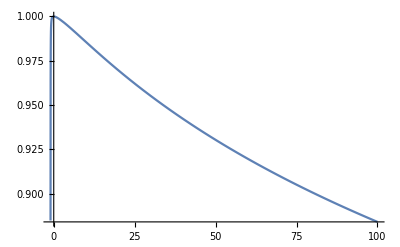

```mathematica
Plot[pudfinal[k,5], {k,-0.99,100}]
```